## Import Data

```mathematica
dat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\test_set_ret_WB.xlsx"];
```

```mathematica
dat//First//Keys//Normal
```

{reaction number,source,class,true reaction smiles,notes}

```mathematica
rxnClasses=Normal[DeleteDuplicates@dat[All,"class"]]
```

{substitution,elimination,grignard,friedelcrafts,asub,dielsalder,amine,carbonylcondensation,organocopper,acetylide}

## IBM Rxn API Wrapper Code - (https://github.com/wrborrelli/IBMRxnAPI)

### Necessary Variable Assignments

```mathematica
(* Initial run of this notebook will prompt you to enter your authorization key. Once you've done that feel free to delete the following cell. *)
```

```mathematica
(*SystemCredential["authKey"]=InputString["Authorization Key"];*)
```

```mathematica
authKey=SystemCredential["authKey"];
```

### Wrapper Code

```mathematica
baseURL="rxn.res.ibm.com";
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
]]
```

```mathematica
(* duplicate of above - for adding a output format parameter *)
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String,outType_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants,rsmiles},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projectID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
]]
```

```mathematica
(* for getting more outcomes from a prediction that you've already made *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest [URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
]]
```

```mathematica
(* duplicate of above - for adding an output type *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String,outType_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rsmilesList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
	Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each rsmiles to the list *)
AppendTo[rsmilesList,getPred["payload","attempts"][[i]]["smiles"]],
{i,1,Length[getPred["payload","attempts"]]}];

rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;

Dataset@MapThread[<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[#1][[1]],"rprod"->reacSplit[#1][[2]],"conf"->#2,"reaction image"->#3|>&,{rsmilesList,rxnConfList,rxnImages}]
]
]]
```

```mathematica
(* for making a new retrosynthesis *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100]},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->"",
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* duplicate of above - added to specify a precursor *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* duplicate of above - added to specify output type *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String,outType_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product,cols,cSMILES,retroID},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* for making a new project, listing all project attempts, or recovering a past prediction or retrosynthesis *)
```

```mathematica
IBMRxn[req_String,IDorName_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* duplicate of above - added to allow for specifying ouput type *)
```

```mathematica
IBMRxn[req_String,IDorName_String,outType_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs,retroID,product,cols,cSMILES,rsmiles},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* just for getting all stored projects. if "stored projects" is given as input, outputs a dataset of all stored projects as well as the total number of projects stored *)
```

```mathematica
IBMRxn[req_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,queueState},
Which[(* If[] you want to get all "stored projects", this code block runs *)
req=="stored projects",
myProjects=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

myProjNames=#["name"]&/@myProjects["payload","content"];
myProjIDs=#["id"]&/@myProjects["payload","content"];

nameRule=("Project Name"->#&/@myProjNames);
idRule=("Project ID"->#&/@myProjIDs);

myProjectsData=
Dataset[
Association[#]&/@Transpose[{nameRule,idRule}]]
TableForm[{{ToString[myProjects["payload","totalElements"]]}},TableHeadings->{None,{"Total Stored Projects"}},TableAlignments->Center]
,
req=="queue status",(* get the status of the retrosynthesis queue *)
queueState=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/queue-state"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

queueState
]]
```

## Helper Functions

```mathematica
(* needed for rxn wrapper - splits reaction strings into reactants and products *)
```

```mathematica
reacSplit[reacs_String]:=StringSplit[reacs,">>"];
```

```mathematica
(* plots a given reaction string *)
```

```mathematica
rxnPlt[rsmiles_String,title_String,rclass_String]:=Module[{plus=Graphics[Text@Style["+",20],BaselinePosition->Center,ImageSize->100],arrow=Graphics[Text@Style["→",20],BaselinePosition->Center,ImageSize->100],reacsplit,reacs,prods,reacPlots,prodPlots},
reacsplit=reacSplit[rsmiles];
reacs=StringSplit[reacsplit[[1]],"."];
prods=StringSplit[reacsplit[[2]],"."];
reacPlots=Table[MoleculePlot[Molecule[i],ImageSize->Large],{i,reacs}];
prodPlots=Table[MoleculePlot[Molecule[j],ImageSize->Large],{j,prods}];
Show[GraphicsRow[Flatten[{Riffle[reacPlots,plus],arrow,Riffle[prodPlots,plus]}],ImageSize->Full,Frame->True],PlotLabel->title<>"\n"<>rclass,LabelStyle->{FontFamily->"Cambria",12,GrayLevel[0]}]
]
```

```mathematica
mapRetros[targetList_,projID_,n_]:=Dataset[Flatten@Normal@ResourceFunction["MapBatched"][Take[IBMRxn["new retrosynthesis",projID,#,"","dataset"],UpTo[n]]&,targetList,Pause[15],1]]
```

```mathematica
(* get predictions for all reactions *)
```

```mathematica
mapFwds[reacsList_,projID_]:=Dataset[Flatten@Normal@ResourceFunction["MapBatched"][IBMRxn["new prediction",#,projID,"dataset"]&,reacsList,Pause[10],1]]
```

```mathematica
(* format all of the prediction and test data into one *)
```

```mathematica
formatDat[testDatReac_,resultsDat_]:=Module[{reacNumb=Normal[testDatReac["reaction number"]],source=Normal[testDatReac["source"]],trclass=Normal[testDatReac["class"]],trsmiles=Normal[testDatReac["true reaction smiles"]],notes=Normal[testDatReac["notes"]],rets,reacNumbs},

rets=resultsDat[Select[#prod==Last[reacSplit[trsmiles]]&]];
reacNumbs=Prepend[Range[reacNumb+0.2,(reacNumb+0.1*Length[rets]),0.1],reacNumb];

Dataset[MapThread[<|
"reaction number"->#1,"true rclass"->#2,"true reaction smiles"->#3,"true prod"->#4,"pred reaction smiles"->#5,"pred prod"->#6,"conf"->#7,"projID"->#8,"retroID"->#9
|>&,{reacNumbs,Table[trclass,{i,1,Length[rets]}],Table[trsmiles,{i,1,Length[rets]}],Table[Last[reacSplit[trsmiles]],{i,1,Length[rets]}],Map[#[[1]]<>">>"<>#[[2]]&,Thread[{Normal[rets[All,"rreac"]],Normal[rets[All,"prod"]]}]],Normal[rets[All,"prod"]],Normal[rets[All,"conf"]],Normal[rets[All,"projID"]],Normal[rets[All,"retroID"]]}]]
]
```

```mathematica
(* format all of the forward prediction and test data into one *)
```

```mathematica
(* test if the molecules are the same with or without stereochemistry *)
```

```mathematica
sameProd[trProd_,prProd_]:=Module[{tprodSt,pprodSt,tprod,pprod},
Which[
Not[StringContainsQ[trProd,"."]],
tprodSt=Molecule[trProd];
pprodSt=Molecule[prProd];
tprod=MoleculeModify[tprodSt,"RemoveStereochemistry"];
pprod=MoleculeModify[pprodSt,"RemoveStereochemistry"];
MoleculeEquivalentQ[tprodSt,pprodSt]||MoleculeEquivalentQ[tprod,pprod]||MoleculeEquivalentQ[tprodSt,pprod]||MoleculeEquivalentQ[tprod,pprodSt]
,
StringContainsQ[trProd,"."],
tprodSt=Map[Molecule[#]&,StringSplit[trProd,"."]];
pprodSt=Molecule[prProd];
tprod=Map[MoleculeModify[#,"RemoveStereochemistry"]&,tprodSt];
pprod=MoleculeModify[pprodSt,"RemoveStereochemistry"];
MemberQ[Map[MoleculeEquivalentQ[#,pprodSt]&,tprodSt],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprod]&,tprod],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprod]&,tprodSt],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprodSt]&,tprod],True]
]]
```

```mathematica
(* check if the predicted product matches the true product *)
```

```mathematica
predProdMatches[dat_,rClass_String]:=Quiet[MapThread[sameProd[#1,#2]&,{Normal[Values@dat[Select[#"true rclass"==rClass&]][All,{"true prod","pred prod"}]][[All,1]],Normal[Values@dat[Select[#"true rclass"==rClass&]][All,{"true prod","pred prod"}]][[All,2]]}]]
```

```mathematica
(* same as above but adds a feature for multiple reactions and taking top k predictions *)
```

```mathematica
predProdMatches[dat_Dataset,rClass_String,k_Integer]:=Module[{maxRNumb,minRNumb,reacs,reacIt},
maxRNumb=IntegerPart[Max[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]]];
minRNumb=Round[Min[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]],1];
reacs=Take[#,UpTo[k]]&/@Table[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][Select[IntegerPart[#"reaction number"]==i&]],{i,Range[minRNumb,maxRNumb]}];
Map[(reacIt=#;
If[Length[reacIt]==1,
Quiet[sameProd[First[reacIt]["true prod"],First[reacIt]["pred prod"]]]
,
MemberQ[Quiet[MapThread[sameProd[#1,#2]&,{Normal[reacIt[All,"true prod"]],Normal[reacIt[All,"pred prod"]]}]],True]
])&,reacs]
]
```

```mathematica
(* molecular complexity difference computation *)
```

```mathematica
compDiff[rSmiles_String]:=Module[{reactants,prod,rComp,pComp},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
prod=StringSplit[reacSplit[rSmiles][[2]],"."];

rComp=Total@Table[If[SameQ[Head[Quiet@MolecularComplexity[reactants[[i]]]],Real],MolecularComplexity[reactants[[i]]],0],{i,1,Length@reactants}];
pComp=Total@Table[If[SameQ[Head[Quiet@MolecularComplexity[prod[[i]]]],Real],MolecularComplexity[prod[[i]]],0],{i,1,Length@prod}];

pComp-rComp
]
```

```mathematica
SetAttributes[compDiff,Listable]
```

```mathematica
Options[MolecularComplexity]={"Stereochemistry"->True};(* options to ignore diastereotopic effects relating to equivalence of bonds *)
```

```mathematica
MolecularComplexity[mol_,OptionsPattern[]]:=Module[{molec=Molecule[mol],aInds,aSyms,indTsym,symAtoms,symAtomsNoH,indTval,indTcon,bondPairs,bondIndPairs,bondIndsNoH,bondIndPairsNoH,ind,jnd,atomI,vi,bi,di,dj,bondedAs,ei,eAs,si,vj,bj,sj,ej,out,terms,atomII,atomIIpos,jnds,nonEqTerms,eqTerms,allTerms,bTypes,sharedA,adjA,aIndsNoH,adjM},
aInds=MoleculeValue[molec,"AtomIndex"];(*  atom indices *)
aIndsNoH=Select[Thread[{MoleculeValue[molec,"AtomicSymbol"],aInds}],Not@MemberQ[#,"H"]&][[All,2]];
aSyms=MoleculeValue[molec,"AtomicSymbol"];
indTsym=AssociationThread[aInds,aSyms];(* atom indices -> atomic symbol *)
symAtoms=MoleculeValue[molec,"SymmetryEquivalentAtoms"];
symAtomsNoH=Select[Thread[{TakeList[aSyms,Length[#]&/@symAtoms],symAtoms}],Not@MemberQ[#[[1]],"H"]&][[All,2]];
adjM=Normal[MoleculeValue[molec,"AdjacencyMatrix"]];
symAtomsNoH=Quiet@If[OptionValue["Stereochemistry"],
symAtomsNoH,
Table[
Which[
Length[m]==1,{m},
Length[m]>1,
sharedA=First@Position[First[Intersection[adjM[[m,aIndsNoH]]]],1];(* gets the atom that the sym atoms share *)
adjA=First@Position[First[adjM[[sharedA,aIndsNoH]]]*Boole[Not@ContainsAny[m,{#}]&/@Range[Length@aIndsNoH]],1];(* gets the atoms that the shared atom is bonded to *)
If[ContainsOnly[Flatten[Position[First[adjM[[sharedA,aIndsNoH]]],1]],m],{m},
If[SameQ[First@Table[MoleculeValue[molec,{"AtomChirality",j}],{j,adjA}],None],{m},Split[m]]
](* tests if those attached atoms are stereocenters *)
]
,{m,symAtomsNoH}]//Flatten[#,1]&
,OptionValue["Stereochemistry"]];(* lists of symmetrically equivalent atoms *)
indTval=AssociationThread[MoleculeValue[molec,"AtomIndex"],MoleculeValue[molec,"OuterShellElectronCount"]];(* atom index -> valence *)
bondPairs=Lookup[indTsym,#]&/@MoleculeValue[molec,"BondedAtomIndices"];(* list of lists of bonded atom indices *)
bondIndPairs=Thread[{bondPairs,MoleculeValue[molec,"BondedAtomIndices"]}];(* list of pairs of {bonded atom symbols, bonded atom indices} *)
bondIndsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&][[All,2]]; (* list of lists of bonded indices with H removed *)
bondIndPairsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&]; 


terms=Table[
atomI=symAtomsNoH[[i]];
If[Length[atomI]==1,(* if there are no equivalent atoms *)

vi=indTval[First[atomI]];
bi=(
bTypes=MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]];
Total[
Which[(* uses rules to case-by-case fix valence and resonance-based bonding equivalencies *)
indTsym[First[atomI]]=="C",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],

indTsym[First[atomI]]=="O"||indTsym[First[atomI]]=="S",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->1}],

indTsym[First[atomI]]=="N",
Which[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==3),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]==1),
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==2),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]],

True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]]
]
);
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

{di,ei,si,vi,bi}
,(* if there is more than 1 equivalent atom *)
vi=indTval[First[atomI]];
bi=(
bTypes=MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]];
Total[
Which[
indTsym[First[atomI]]=="C",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],

indTsym[First[atomI]]=="O"||indTsym[First[atomI]]=="S",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->1}],

indTsym[First[atomI]]=="N",
Which[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==3),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]==1),
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==2),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]],

True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]]
]
);
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

Table[{di,ei,si,vi,bi},Length@atomI]
],{i,1,Length@symAtomsNoH}];

nonEqTerms=Select[terms,Not[MatrixQ[#]]&];
eqTerms=Flatten[Select[terms,MatrixQ[#]&],1];
allTerms=Join[nonEqTerms,eqTerms];

If[Length[eqTerms]>0,
N[Sum[(
allTerms[[All,1]][[s1]]*allTerms[[All,2]][[s1]]*allTerms[[All,3]][[s1]]*Log2[(allTerms[[All,4]][[s1]]*allTerms[[All,5]][[s1]])])
,{s1,1,Length@allTerms}]-0.5*Sum[(eqTerms[[All,1]][[j1]]*eqTerms[[All,2]][[j1]]*eqTerms[[All,3]][[j1]]*Log2[(eqTerms[[All,4]][[j1]]*eqTerms[[All,5]][[j1]])]),{j1,1,Length@eqTerms}]]
,
N[Sum[
allTerms[[All,1]][[s2]]*allTerms[[All,2]][[s2]]*allTerms[[All,3]][[s2]]*Log2[allTerms[[All,4]][[s2]]*allTerms[[All,5]][[s2]]]
,{s2,1,Length@allTerms}]]
]
]
```

```mathematica
SetAttributes[MolecularComplexity,Listable]
```

```mathematica
(* for computing the difference in synthetic accessiblity score *)
```

```mathematica
dSA[rSmiles_String]:=Module[{reactants,products,rSA,pSA},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
products=StringSplit[reacSplit[rSmiles][[2]],"."];
rSA=Total[Table[MoleculeValue[Molecule[i],"SyntheticAccessibilityScore"],{i,reactants}]];
pSA=Total[Table[MoleculeValue[Molecule[i],"SyntheticAccessibilityScore"],{i,products}]];
pSA-rSA
]
```

```mathematica
SetAttributes[dSA,Listable]
```

```mathematica
mapFwds[reacsList_,projID_]:=Dataset[Flatten@Normal@ResourceFunction["MapBatched"][IBMRxn["new prediction",#,projID,"dataset"]&,reacsList,Pause[10],1]]
```

## Get Predictions

Query 5 retrosyntheses for each target in each reaction class.

### Project ID’s

```mathematica
rxnClasses
```

{substitution,elimination,grignard,friedelcrafts,asub,dielsalder,amine,carbonylcondensation,}

```mathematica
(* make a unique project ID for each reaction class *)
```

```mathematica
(*subProjRet=IBMRxn["new project","subRet"];
```

```mathematica
(*subProjID=Flatten[subProjRet[[1]]][[2]]
```

```mathematica
subProjRetID="602c6e63329a1000012c1428";
```

```mathematica
(*elimProjRet=IBMRxn["new project","elimRet"];
```

```mathematica
(*elimProjID=Flatten[elimProjRet[[1]]][[2]]
```

```mathematica
elimProjRetID="602c6e99329a1000012c1439";
```

```mathematica
(*grigProjRet=IBMRxn["new project","grigRet"];
```

```mathematica
(*grigProjID=Flatten[grigProjRet[[1]]][[2]]
```

```mathematica
grigProjRetID="602c6ec6329a1000012c1443";
```

```mathematica
(*fcProjRet=IBMRxn["new project","fcRet"];
```

```mathematica
(*fcProjID=Flatten[fcProjRet[[1]]][[2]]
```

```mathematica
fcProjRetID="602c6eea329a1000012c1455";
```

```mathematica
(*asubProjRet=IBMRxn["new project","asubRet"];
```

```mathematica
(*asubProjID=Flatten[asubProjRet[[1]]][[2]]
```

```mathematica
asubProjRetID="602c6f13329a1000012c1466";
```

```mathematica
(*daProjRet=IBMRxn["new project","daRet"];
```

```mathematica
(*daProjID=Flatten[daProjRet[[1]]][[2]]
```

```mathematica
daProjRetID="602c6f49329a1000012c147a";
```

```mathematica
(*aminProjRet=IBMRxn["new project","aminRet"];
```

```mathematica
(*aminProjID=Flatten[aminProjRet[[1]]][[2]]
```

```mathematica
aminProjRetID="602dcdc7329a1000012d9ee2";
```

```mathematica
(*condProjRet=IBMRxn["new project","condRet"];
```

```mathematica
(*condProjID=Flatten[condProjRet[[1]]][[2]]
```

```mathematica
condProjRetID="6031c42271c8b600012f8277";
```

```mathematica
(*orgProjRet=IBMRxn["new project","orgRet"];
```

```mathematica
(*orgProjRetRetID=Flatten[orgProjRet[[1]]][[2]]
```

```mathematica
orgProjRetID="6034829b71c8b600013313f6";
```

```mathematica
(*acetProjRet=IBMRxn["new project","acetRet"];
```

```mathematica
(*acetProjRetRetID=Flatten[acetProjRet[[1]]][[2]]
```

```mathematica
acetProjRetID="6035b34b71c8b6000134ac42";
```

### Substitution - done

```mathematica
subRxnsRet=Normal[dat[Select[#class=="substitution"&]][All,"true reaction smiles"]];
```

```mathematica
subTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,subRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*subRetros1=mapRetros[subTargetList[[1;;5]],subProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*subRetros2=mapRetros[subTargetList[[6;;]],subProjRetID,5];
```

```mathematica
(*subRetros=Join[subRetros1,subRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\subRetrosAll.csv",subRetros,"CSV"];
```

```mathematica
subRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\subRetrosAll.csv"];
```

```mathematica
(*subDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,subRetros]&,dat[Select[#class=="substitution"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\subDatForm.csv",subDatForm,"CSV"];
```

```mathematica
subDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\subDatForm.csv"];
```

### Elimination - done

```mathematica
elimRxnsRet=Normal[dat[Select[#class=="elimination"&]][All,"true reaction smiles"]];
```

```mathematica
elimTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,elimRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*elimRetros1=mapRetros[elimTargetList[[1;;5]],elimProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*elimRetros2=mapRetros[elimTargetList[[6;;]],elimProjRetID,5];
```

```mathematica
(*elimRetros=Join[elimRetros1,elimRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\elimRetrosAll.csv",elimRetros,"CSV"];
```

```mathematica
elimRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\elimRetrosAll.csv"];
```

```mathematica
(*elimDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,elimRetros]&,dat[Select[#class=="elimination"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\elimDatForm.csv",elimDatForm,"CSV"];
```

```mathematica
elimDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\elimDatForm.csv"];
```

### Grignard - done

```mathematica
grigRxnsRet=Normal[dat[Select[#class=="grignard"&]][All,"true reaction smiles"]];
```

```mathematica
grigTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,grigRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*grigRetros1=mapRetros[grigTargetList[[1;;5]],grigProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*grigRetros2=mapRetros[grigTargetList[[6;;]],grigProjRetID,5];
```

```mathematica
(*grigRetros=Join[grigRetros1,grigRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\grigRetrosAll.csv",grigRetros,"CSV"];
```

```mathematica
grigRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\grigRetrosAll.csv"];
```

```mathematica
(*grigDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,grigRetros]&,dat[Select[#class=="grignard"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\grigDatForm.csv",grigDatForm,"CSV"];
```

```mathematica
grigDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\grigDatForm.csv"];
```

### Friedel Crafts - done

```mathematica
fcRxnsRet=Normal[dat[Select[#class=="friedelcrafts"&]][All,"true reaction smiles"]];
```

```mathematica
fcTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,fcRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*fcRetros1=mapRetros[fcTargetList[[1;;5]],fcProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*fcRetros2=mapRetros[fcTargetList[[6;;]],fcProjRetID,5];
```

```mathematica
(*fcRetros=Join[fcRetros1,fcRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\fcRetrosAll.csv",fcRetros,"CSV"];
```

```mathematica
fcRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\fcRetrosAll.csv"];
```

```mathematica
(*fcDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,fcRetros]&,dat[Select[#class=="friedelcrafts"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\fcDatForm.csv",fcDatForm,"CSV"];
```

```mathematica
fcDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\fcDatForm.csv"];
```

### Aromatic Substitution - done

```mathematica
asubRxnsRet=Normal[dat[Select[#class=="asub"&]][All,"true reaction smiles"]];
```

```mathematica
asubTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,asubRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*asubRetros1=mapRetros[asubTargetList[[1;;5]],asubProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*asubRetros2=mapRetros[asubTargetList[[6;;]],asubProjRetID,5];
```

```mathematica
(*asubRetros=Join[asubRetros1,asubRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\asubRetrosAll.csv",asubRetros,"CSV"];
```

```mathematica
asubRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\asubRetrosAll.csv"];
```

```mathematica
(*asubDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,asubRetros]&,dat[Select[#class=="asub"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\asubDatForm.csv",asubDatForm,"CSV"];
```

```mathematica
asubDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\asubDatForm.csv"];
```

### Diels Alder - done

```mathematica
daRxnsRet=Normal[dat[Select[#class=="dielsalder"&]][All,"true reaction smiles"]];
```

```mathematica
daTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,daRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*daRetros1=mapRetros[daTargetList[[1;;5]],daProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*daRetros2=mapRetros[daTargetList[[6;;]],daProjRetID,5];
```

```mathematica
(*daRetros=Join[daRetros1,daRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\daRetrosAll.csv",daRetros,"CSV"];
```

```mathematica
daRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\daRetrosAll.csv"];
```

```mathematica
(*daDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,daRetros]&,dat[Select[#class=="dielsalder"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\daDatForm.csv",daDatForm,"CSV"];
```

```mathematica
daDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\daDatForm.csv"];
```

### Amine - done

```mathematica
aminRxnsRet=Normal[dat[Select[#class=="amine"&]][All,"true reaction smiles"]];
```

```mathematica
aminTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,aminRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*aminRetros1=mapRetros[aminTargetList[[1;;5]],aminProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*aminRetros2=mapRetros[aminTargetList[[6;;]],aminProjRetID,5];
```

```mathematica
(*aminRetros=Join[aminRetros1,aminRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\aminRetrosAll.csv",aminRetros,"CSV"];
```

```mathematica
aminRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\aminRetrosAll.csv"];
```

```mathematica
(*aminDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,aminRetros]&,dat[Select[#class=="amine"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\aminDatForm.csv",aminDatForm,"CSV"];
```

```mathematica
aminDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\aminDatForm.csv"];
```

### Carbonyl Condensation - done

```mathematica
condRxnsRet=Normal[dat[Select[#class=="carbonylcondensation"&]][All,"true reaction smiles"]];
```

```mathematica
condTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,condRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*condRetros1=mapRetros[condTargetList[[1;;5]],condProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*condRetros2=mapRetros[condTargetList[[6;;]],condProjRetID,5];
```

```mathematica
(*condRetros=Join[condRetros1,condRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\condRetrosAll.csv",condRetros,"CSV"];
```

```mathematica
(*condRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\condRetrosAll.csv"];
```

```mathematica
condDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,condRetros]&,dat[Select[#class=="carbonylcondensation"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\condDatForm.csv",condDatForm,"CSV"];
```

```mathematica
condDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\condDatForm.csv"];
```

### Organocopper - done

```mathematica
orgRxnsRet=Normal[dat[Select[#class=="organocopper"&]][All,"true reaction smiles"]];
```

```mathematica
orgTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,orgRxnsRet][[All,2]]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*orgRetros1=mapRetros[orgTargetList[[1;;5]],orgProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*orgRetros2=mapRetros[orgTargetList[[6;;]],orgProjRetID,5];
```

```mathematica
(*orgRetros=Join[orgRetros1,orgRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\orgRetrosAll.csv",orgRetros,"CSV"];
```

```mathematica
orgRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\orgRetrosAll.csv"];
```

```mathematica
(*orgDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,orgRetros]&,dat[Select[#class=="organocopper"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\orgDatForm.csv",orgDatForm,"CSV"];
```

```mathematica
orgDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\orgDatForm.csv"];
```

### Acetylide - done

```mathematica
acetRxnsRet=Normal[dat[Select[#class=="acetylide"&]][All,"true reaction smiles"]];
```

```mathematica
acetTargetList=Map[StringSplit[#,"."]&,Map[StringSplit[#,">>"]&,acetRxnsRet][[All,2]]];
```

```mathematica
(*Pause[300];
```

```mathematica
(*acetRetros1=mapRetros[acetTargetList[[1;;5]],acetProjRetID,5];
```

```mathematica
(*Pause[120]
```

```mathematica
(*acetRetros2=mapRetros[acetTargetList[[6;;]],acetProjRetID,5];
```

```mathematica
(*acetRetros=Join[acetRetros1,acetRetros2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\acetRetrosAll.csv",acetRetros,"CSV"];
```

```mathematica
acetRetros=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\acetRetrosAll.csv"];
```

```mathematica
(*acetDatForm=Dataset[Flatten@Normal@Normal@Map[formatDat[#,acetRetros]&,dat[Select[#class=="acetylide"&]]]];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\acetDatForm.csv",acetDatForm,"CSV"];
```

```mathematica
acetDatForm=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\all_preds\\acetDatForm.csv"];
```

### Combine Data

```mathematica
(*combDatAllRet=Join[subDatForm,elimDatForm,grigDatForm,fcDatForm,asubDatForm,daDatForm,aminDatForm,condDatForm,orgDatForm,acetDatForm];
```

```mathematica
(*combDatRet=Dataset[Flatten@Normal@Table[Select[combDatAllRet,#["reaction number"]==i&],{i,Range[Length[DeleteDuplicates@combDatAllRet[All,"true prod"]]]}]];
```

```mathematica
combDatAllRet=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\combDatAllRet.csv"];
```

```mathematica
combDatRet=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\combDatRet.csv"];
```

## Get Forward Predictions of Predicted Syntheses

```mathematica
combDatRet//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,retroID}

```mathematica
(* all first predicted synthesis reactions *)
```

```mathematica
{subFwdRxns,elimFwdRxns,grigFwdRxns,fcFwdRxns,asubFwdRxns,daFwdRxns,aminFwdRxns,condFwdRxns,orgFwdRxns,acetFwdRxns}=Values[Normal[combDatRet[All,{"true rclass","pred reaction smiles"}][GroupBy[#"true rclass"&]][All,All,"pred reaction smiles"]]];
```

```mathematica
(* just the reactants *)
```

```mathematica
{subFwdReacs,elimFwdReacs,grigFwdReacs,fcFwdReacs,asubFwdReacs,daFwdReacs,aminFwdReacs,condFwdReacs,orgFwdReacs,acetFwdReacs}=Map[StringSplit[#,"."]&,Map[reacSplit[#]&,#][[All,1]]]&/@{subFwdRxns,elimFwdRxns,grigFwdRxns,fcFwdRxns,asubFwdRxns,daFwdRxns,aminFwdRxns,condFwdRxns,orgFwdRxns,acetFwdRxns};
```

### Substitution - done

```mathematica
(*subFwds1=mapFwds[subFwdReacs[[1;;5]],subProjRetID];
```

```mathematica
(*Pause[120];
```

```mathematica
(*subFwds2=mapFwds[subFwdReacs[[6;;]],subProjRetID];
```

```mathematica
(*subFwds=Join[subFwds1,subFwds2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\subFwdPreds.csv",subFwds,"CSV"];
```

```mathematica
subFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\subFwdPreds.csv",HeaderLines->1];
```

### Elimination

```mathematica
(*Pause[300];
```

```mathematica
(*elimFwds1=mapFwds[elimFwdReacs[[1;;5]],elimProjRetID];
```

```mathematica
(*Pause[300];
```

```mathematica
(*elimFwds2=mapFwds[elimFwdReacs[[6;;]],elimProjRetID];
```

```mathematica
(*elimFwds=Join[elimFwds1,elimFwds2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\elimFwdPreds.csv",elimFwds,"CSV"];
```

```mathematica
elimFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\elimFwdPreds.csv",HeaderLines->1];
```

### Grignard - done

```mathematica
(*Pause[300];
```

```mathematica
(*grigFwds1=mapFwds[grigFwdReacs[[1;;5]],grigProjRetID];
```

```mathematica
(*Pause[120];
```

```mathematica
(*grigFwds2=mapFwds[grigFwdReacs[[6;;]],grigProjRetID];
```

```mathematica
(*grigFwds=Join[grigFwds1,grigFwds2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\grigFwdPreds.csv",grigFwds,"CSV"];
```

```mathematica
grigFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\grigFwdPreds.csv",HeaderLines->1];
```

### Friedel Crafts - done

```mathematica
(*Pause[300];
```

```mathematica
(*fcFwds1=mapFwds[fcFwdReacs[[1;;5]],fcProjRetID];
```

```mathematica
(*Pause[120];
```

```mathematica
(*fcFwds2=mapFwds[fcFwdReacs[[6;;]],fcProjRetID];
```

```mathematica
(*fcFwds=Join[fcFwds1,fcFwds2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\fcFwdPreds.csv",fcFwds,"CSV"];
```

```mathematica
fcFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\fcFwdPreds.csv",HeaderLines->1];
```

### Aromatic Substitution - done

```mathematica
(*Pause[300];
```

```mathematica
(*asubFwds1=Quiet[mapFwds[asubFwdReacs[[1;;5]],asubProjRetID]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*asubFwds2=Quiet[mapFwds[asubFwdReacs[[6;;]],asubProjRetID]];
```

```mathematica
(*asubFwds=Join[asubFwds1,asubFwds2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\asubFwdPreds.csv",asubFwds,"CSV"];
```

```mathematica
asubFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\asubFwdPreds.csv",HeaderLines->1];
```

### Diels Alder - done

```mathematica
(*Pause[300];
```

```mathematica
(*daFwds1=mapFwds[daFwdReacs[[1;;5]],daProjRetID];
```

```mathematica
(*Pause[120];
```

```mathematica
(*daFwds2=mapFwds[daFwdReacs[[6;;]],daProjRetID];
```

```mathematica
(*daFwds=Join[daFwds1,daFwds2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\daFwdPreds.csv",daFwds,"CSV"];
```

```mathematica
daFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\daFwdPreds.csv",HeaderLines->1];
```

### Amine - done

```mathematica
(*Pause[300];
```

```mathematica
(*aminFwds1=Quiet[mapFwds[aminFwdReacs[[1;;5]],aminProjRetID]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*aminFwds2=Quiet[mapFwds[aminFwdReacs[[6;;]],aminProjRetID]];
```

```mathematica
(*aminFwds=Join[aminFwds1,aminFwds2];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\aminFwdPreds.csv",aminFwds,"CSV"];
```

```mathematica
aminFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\aminFwdPreds.csv",HeaderLines->1];
```

### Carbonyl Condensation - done

```mathematica
(*Pause[300];
```

```mathematica
(*condFwds1=Quiet[mapFwds[condFwdReacs[[1;;5]],condProjRetID]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*condFwds2=Quiet[mapFwds[condFwdReacs[[6;;]],condProjRetID]];
```

```mathematica
(*condFwds=Join[condFwds1,condFwds2];
```

```mathematica
(*Quiet[Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\condFwdPreds.csv",condFwds,"CSV"]];
```

```mathematica
condFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\condFwdPreds.csv",HeaderLines->1];
```

### Organocopper - done

```mathematica
(*Pause[300];
```

```mathematica
(*orgFwds1=Quiet[mapFwds[orgFwdReacs[[1;;5]],orgProjRetID]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*orgFwds2=Quiet[mapFwds[orgFwdReacs[[6;;]],orgProjRetID]];
```

```mathematica
(*orgFwds=Join[orgFwds1,orgFwds2];
```

```mathematica
(*Quiet[Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\orgFwdPreds.csv",orgFwds,"CSV"]];
```

```mathematica
orgFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\orgFwdPreds.csv",HeaderLines->1];
```

### Acetylide - done

```mathematica
(*Pause[300];
```

```mathematica
(*acetFwds1=Quiet[mapFwds[acetFwdReacs[[1;;5]],acetProjRetID]];
```

```mathematica
(*Pause[120];
```

```mathematica
(*acetFwds2=Quiet[mapFwds[acetFwdReacs[[6;;]],acetProjRetID]];
```

```mathematica
(*acetFwds=Join[acetFwds1,acetFwds2];
```

```mathematica
(*Quiet[Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\acetFwdPreds.csv",acetFwds,"CSV"]];
```

```mathematica
acetFwds=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\fwd_preds\\acetFwdPreds.csv",HeaderLines->1];
```

### Combine Data

```mathematica
(*allFwdDat=Join[subFwds,elimFwds,grigFwds,fcFwds,asubFwds,daFwds,aminFwds,condFwds,orgFwds,acetFwds];
```

```mathematica
(*combFwdDat=Dataset@MapThread[<|
"reaction number"->#1,
"true rclass"->#2,
"true reaction smiles"->#3,
"pred reaction smiles"->#4,
"true prod"->#5,
"pred prod"->#6,
"conf"->#7,
"projID"->#8,
"predID"->#9
|>&,{Normal[combDatRet[All,"reaction number"]],Normal[combDatRet[All,"true rclass"]],Normal[combDatRet[All,"true reaction smiles"]],Normal[combDatRet[All,"pred reaction smiles"]],Normal[combDatRet[All,"true prod"]],Normal[allFwdDat[All,"rprod"]],Normal[allFwdDat[All,"conf"]],Normal[allFwdDat[All,"projID"]],Normal[allFwdDat[All,"predID"]]}];
```

```mathematica
(*Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\combFwdDat.csv",combFwdDat,"CSV"];
```

```mathematica
combFwdDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\combFwdDat.csv"];
```

## Distribution Based Analyses

```mathematica
combDatRet//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,retroID}

```mathematica
(* distribution of confidence scores *)
```

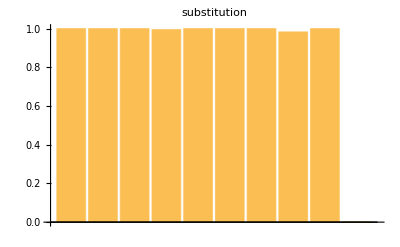
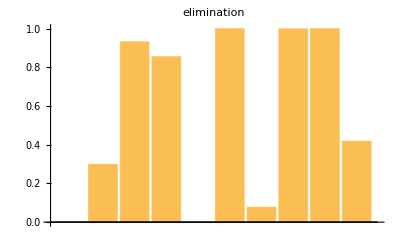
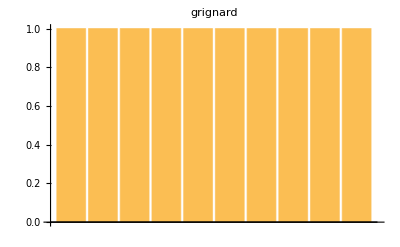
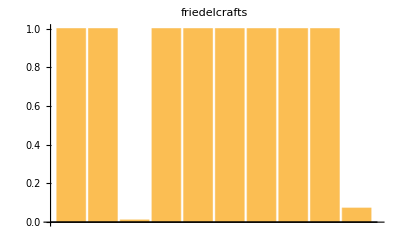
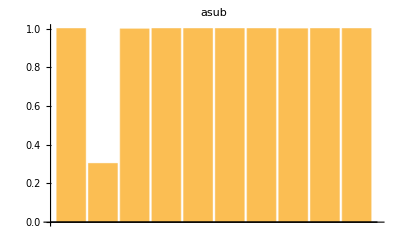
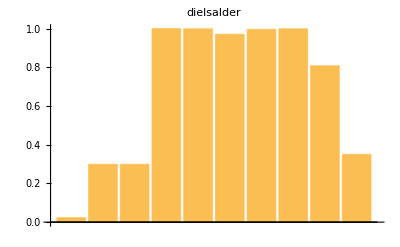
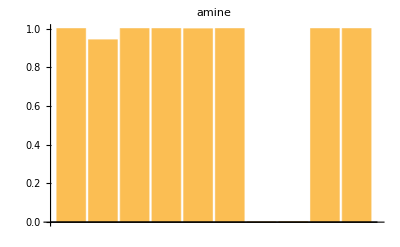
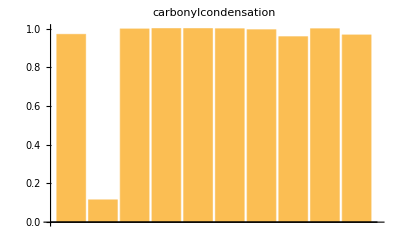

```mathematica
BarChart[#[[2]],PlotLabel->#[[1]]]&/@Thread[{Normal[Keys@combDatRet[All,{"true rclass","conf"}][GroupBy[#"true rclass"&]][All,All,"conf"]],Normal[Values@combDatRet[All,{"true rclass","conf"}][GroupBy[#"true rclass"&]][All,All,"conf"]]}]
```

## Low Confidence Reactions

### Substitution - 1 candidate

```mathematica
(* only reaction 10 is very low *)
```

```mathematica
subLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[1]],#conf&][[1]];
```

```mathematica
(* true and pred retro *)
```

```mathematica
MapThread[rxnPlt[#1,"",#2]&,{Normal[Values@subLC[{"true reaction smiles","pred reaction smiles"}]],{"true retro","pred retro"}}];
```

### Elimination - 5 candidates

```mathematica
(* take ones w/ conf < 0.5 *)
```

```mathematica
elimLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[2]],#conf&][[1;;5]];
```

```mathematica
(* true and pred retro *)
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@elimLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 15: doesn’t seem to obey atom conservation
reaction 11: doesn’t seem to make sense
reaction 17: nonsensical, maybe no atom conservation (but stoichiometric) 
reaction 12: reduction of benzene with H_2 to cyclohexene (unlikely) 
reaction 20: reduction of benzene to the diene (likely)

### Grignard - 0 low confidence

```mathematica
grigLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[3]],#conf&];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@grigLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

### Friedel Crafts - 2 candidates

```mathematica
(* take those less than 0.5 *)
```

```mathematica
fcLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[4]],#conf&][[1;;2]]
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@fcLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 33: will probably work but starts with tosyl toluene to make toluene 
reaction 40: does an aromatic sub, meta to an activating o,p director

### Aromatic Substitution - 1 candidate

```mathematica
(* take those less than 0.5 *)
```

```mathematica
asubLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[5]],#conf&][[1]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&@Normal[Values@asubLC[{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{-Graphics-,-Graphics-}

reaction 42: probably work, very intense compared to acid catalyzed nitration

### Diels Alder - 4 candidates

```mathematica
daLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[6]],#conf&][[1;;4]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@daLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 51: exactly correct, just low confidence
reaction 52: again, reduction of benzene to cyclohexene (unlikely) 
reaction 53: just oxidizes a carbonyl on the starting material (probably work fine) 
reaction 60: unsure, some reaction with Cl2 and SnCl4

### Amine - 2 (weak) candidates

```mathematica
aminLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[7]],#conf&][[1;;2]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@aminLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 67: exactly correct, but low confidence
rxn 68: acid catalyzed ester hydrolysis (will work)

### Carbonyl Condensation - 1 candidate

```mathematica
condLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[8]],#conf&][[1]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&@Normal[Values@condLC[{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{-Graphics-,-Graphics-}

reaction 72: some kind of oxidation

### Organocopper - 0 low confidence

```mathematica
orgLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[9]],#conf&];
```

### Acetylide - 1 candidate

```mathematica
acetLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[10]],#conf&][[1]];
```

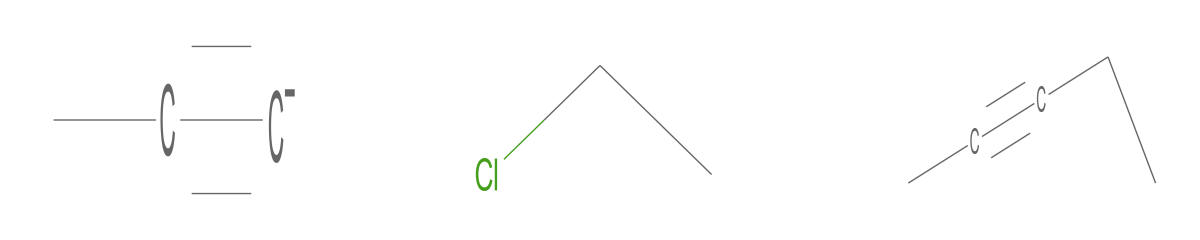
{-Graphics-,-Graphics-}

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&@Normal[Values@acetLC[{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

reaction 92: atom conservation not observed